## B - spline

```mathematica
Subscript[P, 0] = {{0},{0}};
(*Subscript[P, 1] = {{0.5},{0.5}};*)
Subscript[P, 1]= {Sqrt[(0-1)^2]/2,Sqrt[(0-53)^2]/2};
Subscript[P, 2] = {{1},{53}};
Subscript[Q, 0] = Subscript[P, 2];
Subscript[Q, 2] = {{80},{-32}};
Subscript[R, 0] = Subscript[Q, 2];
Subscript[R, 2] = {{62},{20}};
```

### Parametrico

```mathematica
Subscript[P, i_] := {{Subscript[a, i]},{Subscript[b, i]}}
```

```mathematica
Subscript[Q, i_] := {{Subscript[c, i]},{Subscript[d, i]}}
```

```mathematica
Subscript[R, i_] := {{Subscript[e, i]},{Subscript[f, i]}}
```

```mathematica
Subscript[P, 1]
```

{1/2,53/2}

```mathematica
Subscript[P, 2]
```

{{1},{53}}

```mathematica
Subscript[R, 1]
```

{{e_1},{f_1}}

```mathematica
Subscript[B, 1]= Binomial[2,0]*Subscript[P, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[P, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[P, 2]*(1-l)^0*l^2
```

{{(1-l) l+l^2},{53 (1-l) l+53 l^2}}

```mathematica
Subscript[B, 2]= Binomial[2,0]*Subscript[Q, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[Q, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[Q, 2]*(1-l)^0*l^2
```

{{(1-l)^2+80 l^2+2 (1-l) l c_1},{53 (1-l)^2-32 l^2+2 (1-l) l d_1}}

```mathematica
Subscript[dB, 1] = D[Subscript[B, 1],l]
```

{{1},{53 (1-l)+53 l}}

```mathematica
Subscript[dB, 2] = D[Subscript[B, 2],l]
```

{{-2 (1-l)+160 l+2 (1-l) c_1-2 l c_1},{-106 (1-l)-64 l+2 (1-l) d_1-2 l d_1}}

```mathematica
eq = Flatten[(Subscript[dB, 1]/.l-> 1)] - Flatten[(Subscript[dB, 2]/.l-> 0) ]
```

{3-2 c_1,159-2 d_1}

```mathematica
sol = Solve[eq == 0]
```

{{c_1→3/2,d_1→159/2}}

```mathematica
Subscript[curva, 1] = Subscript[B, 1]
```

{{(1-l) l+l^2},{53 (1-l) l+53 l^2}}

```mathematica
Subscript[curva, 2] = Subscript[B, 2]/.sol
```

{{{(1-l)^2+3 (1-l) l+80 l^2},{53 (1-l)^2+159 (1-l) l-32 l^2}}}

```mathematica
(Subscript[B, 1]) // MatrixForm
```

((1-l) l+l^2
53 (1-l) l+53 l^2)

```mathematica
(Subscript[B, 2]) // MatrixForm
```

((1-l)^2+80 l^2+2 (1-l) l c_1
53 (1-l)^2-32 l^2+2 (1-l) l d_1)

```mathematica
Subscript[Q, 1]/.sol
```

{{{3/2},{159/2}}}

```mathematica
Subscript[B, 3]= Binomial[2,0]*Subscript[R, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[R, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[R, 2]*(1-l)^0*l^2
```

{{80 (1-l)^2+62 l^2+2 (1-l) l e_1},{-32 (1-l)^2+20 l^2+2 (1-l) l f_1}}

```mathematica
Subscript[dB, 3] = D[Subscript[B, 3],l]
```

{{-160 (1-l)+124 l+2 (1-l) e_1-2 l e_1},{64 (1-l)+40 l+2 (1-l) f_1-2 l f_1}}

```mathematica
eeq = Flatten[(Subscript[dB, 2]/.l-> 1)] - Flatten[(Subscript[dB, 3]/.l-> 0) ]
sol1 = Solve[eeq == 0]
```

{320-2 c_1-2 e_1,-128-2 d_1-2 f_1}

{{e_1→160-c_1,f_1→-64-d_1}}

```mathematica
sol1 = sol1/. sol
```

{{{e_1→317/2,f_1→-287/2}}}

```mathematica
Subscript[curva, 3] = Subscript[B, 3]/.sol1
```

{{{{80 (1-l)^2+317 (1-l) l+62 l^2},{-32 (1-l)^2-287 (1-l) l+20 l^2}}}}

### Grafico

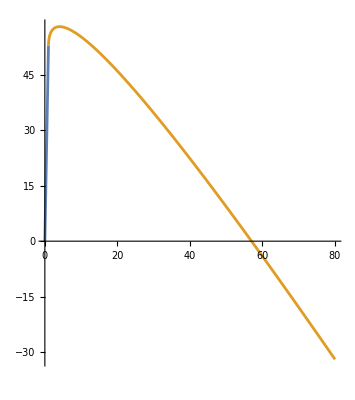

```mathematica
f[l_]:={{1. (1-l) l+l^2},{1. (1-l) l+2 l^2}};
f[l_] := Subscript[curva, 1]
f1[l_] := Subscript[curva, 2]
f2[l_] := Subscript[curva, 3]
ParametricPlot[{f[l],f1[l]},{l,0,1}]
```

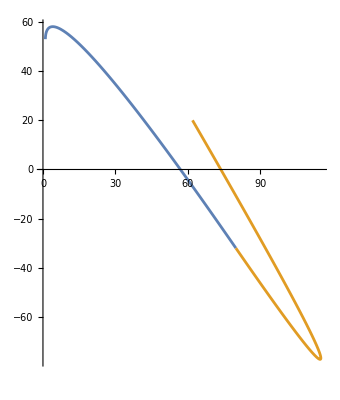

```mathematica
ParametricPlot[{f1[l],f2[l]},{l,0,1}]
```

### Parametrico

```mathematica
Subscript[P, i_] := {{Subscript[a, i]},{Subscript[b, i]}}
```

```mathematica
Subscript[Q, i_] := {{Subscript[c, i]},{Subscript[d, i]}}
```

```mathematica
Subscript[P, 1]
```

{{a_1},{b_1}}

```mathematica
Subscript[P, 2]
```

{{a_2},{b_2}}

```mathematica
Subscript[B, 1]= Binomial[2,0]*Subscript[P, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[P, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[P, 2]*(1-l)^0*l^2
```

{{(1-l)^2 a_0+2 (1-l) l a_1+l^2 a_2},{(1-l)^2 b_0+2 (1-l) l b_1+l^2 b_2}}

```mathematica
Subscript[B, 2]= Binomial[2,0]*Subscript[Q, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[Q, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[Q, 2]*(1-l)^0*l^2
```

{{(1-l)^2 c_0+2 (1-l) l c_1+l^2 c_2},{(1-l)^2 d_0+2 (1-l) l d_1+l^2 d_2}}

```mathematica
Subscript[dB, 1] = D[Subscript[B, 1],l]
```

{{-2 (1-l) a_0+2 (1-l) a_1-2 l a_1+2 l a_2},{-2 (1-l) b_0+2 (1-l) b_1-2 l b_1+2 l b_2}}

```mathematica
Subscript[dB, 2] = D[Subscript[B, 2],l]
```

{{-2 (1-l) c_0+2 (1-l) c_1-2 l c_1+2 l c_2},{-2 (1-l) d_0+2 (1-l) d_1-2 l d_1+2 l d_2}}

```mathematica
eq = Flatten[(Subscript[dB, 1]/.l-> 1)] - Flatten[(Subscript[dB, 2]/.l-> 0) ]
```

{-2 a_1+2 a_2+2 c_0-2 c_1,-2 b_1+2 b_2+2 d_0-2 d_1}

```mathematica
sol = Solve[eq == 0]
```

{{c_1→-a_1+a_2+c_0,d_1→-b_1+b_2+d_0}}

```mathematica
Subscript[curva, 1] = Subscript[B, 1]
```

{{(1-l)^2 a_0+2 (1-l) l a_1+l^2 a_2},{(1-l)^2 b_0+2 (1-l) l b_1+l^2 b_2}}

```mathematica
Subscript[curva, 2] = Subscript[B, 2]/.sol
```

{{{(1-l)^2 c_0+2 (1-l) l (-a_1+a_2+c_0)+l^2 c_2},{(1-l)^2 d_0+2 (1-l) l (-b_1+b_2+d_0)+l^2 d_2}}}

```mathematica
(Subscript[B, 1]) // MatrixForm
```

((1-l)^2 a_0+2 (1-l) l a_1+l^2 a_2
(1-l)^2 b_0+2 (1-l) l b_1+l^2 b_2)

```mathematica
(Subscript[B, 2]) // MatrixForm
```

((1-l)^2 c_0+2 (1-l) l c_1+l^2 c_2
(1-l)^2 d_0+2 (1-l) l d_1+l^2 d_2)

```mathematica
Subscript[Q, 1]/.sol
```

{{{-a_1+a_2+c_0},{-b_1+b_2+d_0}}}